## 5 - calculating linear weights

```mathematica
c1=({{1/Sqrt[2]}, {1/Sqrt[2]}})
c2=({{1/Sqrt[2]}, {-1/Sqrt[2]}})
```

{{1/(√2)},{1/(√2)}}

{{1/(√2)},{-1/(√2)}}

```mathematica
q=({{2}, {3}})
```

{{2},{3}}

## 6 - orthonormal

```mathematica
Vector[S_,Q_]:=(1/Sqrt[S])(Table[E^(I*2*Pi*Q/S(N-1)),{N,0,S-1}])
```

```mathematica
i=0;
k=1;
vi=Vector[8,i]
vk=Vector[8,k]
```

{1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2)}

{ⅇ^(-(ⅈ π)/4)/(2 √2),1/(2 √2),ⅇ^((ⅈ π)/4)/(2 √2),ⅈ/(2 √2),ⅇ^((3 ⅈ π)/4)/(2 √2),-1/(2 √2),ⅇ^(-(3 ⅈ π)/4)/(2 √2),-ⅈ/(2 √2)}

```mathematica
sum=(#1+#2)&[vi,vk]
```

{1/(2 √2)+ⅇ^(-(ⅈ π)/4)/(2 √2),1/(√2),1/(2 √2)+ⅇ^((ⅈ π)/4)/(2 √2),(1/2+ⅈ/2)/(√2),1/(2 √2)+ⅇ^((3 ⅈ π)/4)/(2 √2),0,1/(2 √2)+ⅇ^(-(3 ⅈ π)/4)/(2 √2),(1/2-ⅈ/2)/(√2)}

```mathematica
data=Transpose@{Re[sum],Im[sum]}
```

{{1/4+1/(2 √2),-1/4},{1/(√2),0},{1/4+1/(2 √2),1/4},{1/(2 √2),1/(2 √2)},{-1/4+1/(2 √2),1/4},{0,0},{-1/4+1/(2 √2),-1/4},{1/(2 √2),-1/(2 √2)}}

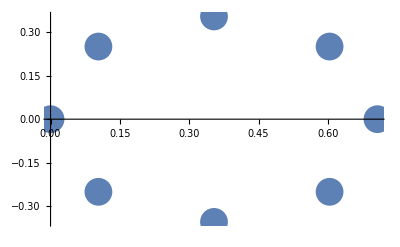

```mathematica
ListPlot[data,PlotStyle->PointSize[.05]]
```

```mathematica
N@Total[sum]
```

2.82843+0. ⅈ

```mathematica
vi=Transpose[{vi}];
vk=Transpose[{vk}];
```

```mathematica
Chop[N@ConjugateTranspose[vi].vk]
```

{{0}}

## 8 - dotting a unit vector with itself is 1

```mathematica
vector=({{1, 2, 34, 5, 6}})
```

{{1,2,34,5,6}}

```mathematica
vector=vector/Norm[vector]
```

{{1/(√1222),√(2/611),17 √(2/611),5/(√1222),3 √(2/611)}}

```mathematica
vector.Transpose@vector
```

{{1}}

## 11 - calculate the 64 point dft of a cos of frequency pi/4 radians

```mathematica
numberSamples=64;
numberRange=Range[0, numberSamples-1];
x=Cos[Pi/4 * numberRange];
DFT=FourierMatrix[numberSamples];
```

```mathematica
xDFT=DFT.x
```

{0,ⅇ^(-(ⅈ π)/32)/(8 √2)+65+ⅇ^(-(31 ⅈ π)/32)/(8 √2)+ⅇ^((31 ⅈ π)/32)/(8 √2),ⅇ^(-1/16)/(4 √2)+29+ⅇ^1/(4 1)+ⅇ^(1/16)/(4 √2),58,1,ⅇ^(-(ⅈ π)/16)/(4 √2)+29+ⅇ^(-1/16)/(4 √2)+ⅇ^((15 11π)/16)/(4 √2),ⅇ^(-(ⅈ π)/32)/(8 √2)+ⅇ^((ⅈ π)/32)/(8 √2)-ⅇ^(-(3 ⅈ π)/32)/(8 √2)-ⅇ^((3 ⅈ π)/32)/(8 √2)-1/8 ⅇ^(-(ⅈ π)/8)-1/8 ⅇ^((ⅈ π)/8)-ⅇ^(-(5 ⅈ π)/32)/(8 √2)-ⅇ^((5 ⅈ π)/32)/(8 √2)+ⅇ^(-(7 ⅈ π)/32)/(8 √2)+51+ⅇ^(-(31 ⅈ π)/32)/(8 √2)+ⅇ^((31 ⅈ π)/32)/(8 √2)}
 |  |  |  |

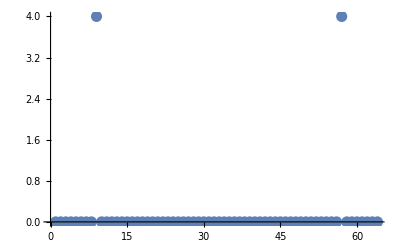

```mathematica
ListPlot[xDFT,PlotStyle->PointSize[.02]]
```

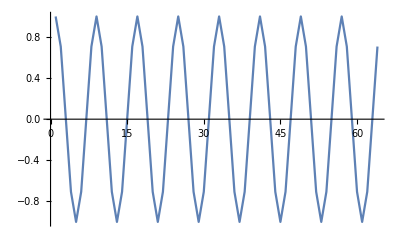

```mathematica
ListLinePlot[x]
```

## 13 - low pass using fourier and inverse fourier

```mathematica
Fs=8192
y=Flatten[Transpose[Import["/home/nathan/olin/fall2016/QEAFall2016Homework/bset1/matlab/handel.csv"]]];
```

8192

```mathematica
Dimensions[y]
```

{73113}

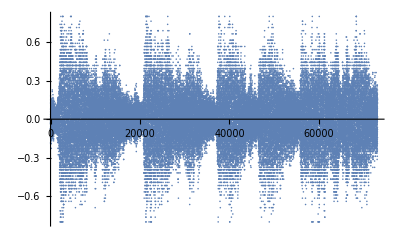

```mathematica
ListPlot[y]
```

### highest frequency

```mathematica
Fs/2
```

4096

### lowest frequency

```mathematica
0
```

0

```mathematica
ListPlay[y,SampleRate->Fs]
```

-Graphics-

```mathematica
fy=Fourier[y]
```

{0.673521-7.88341×10^-17 ⅈ,0.00796712-0.00342063 ⅈ,0.000655436-0.00454289 ⅈ,-0.00464313-0.00121327 ⅈ,73106,-0.00464313+0.00121327 ⅈ,0.000655436+0.00454289 ⅈ,0.00796712+0.00342063 ⅈ}
 |  |  |  |

```mathematica
fyModified=Join[fy[[;;Fs/4-1]],.01*fy[[Fs/4;;]]]
Dimensions[fy]
Dimensions[fyModified]
```

{0.673521-7.88341×10^-17 ⅈ,0.00796712-0.00342063 ⅈ,0.000655436-0.00454289 ⅈ,-0.00464313-0.00121327 ⅈ,73106,-0.0000464313+0.0000121327 ⅈ,6.55436×10^-6+0.0000454289 ⅈ,0.0000796712+0.0000342063 ⅈ}
 |  |  |  |

{73113}

{73113}

```mathematica
yNew=Re[Chop[InverseFourier[fyModified]]]
```

{0.00124555,0.000319132,-0.0012243,-0.00162403,-0.00206683,-0.00253504,-0.00348052,-0.00463178,73097,0.00725178,0.00730997,0.00784001,0.00715208,0.00595054,0.00611754,0.00448704,0.0021147}
 |  |  |  |

```mathematica
ListPlay[y]
```

-Graphics-

```mathematica
ListPlay[yNew]
```

-Graphics-